### Question 1.

```mathematica
t0 = 3.15 * 10^1;
xht = 2.01 * 10^5;
xcp = 3.08 * 10^3;
xhl = -1.05 * 10^4;
p0 = 1.15 * 10^-4;
h0 = 5.25 * 10^-5;
k0 = 1.25 * 10^4;
r0 = 2.25;
n0 = 2.75 * 10^2;
```

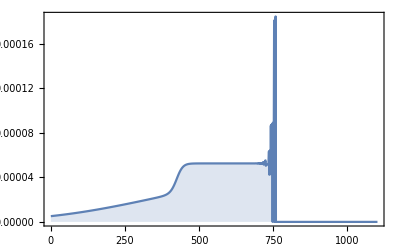

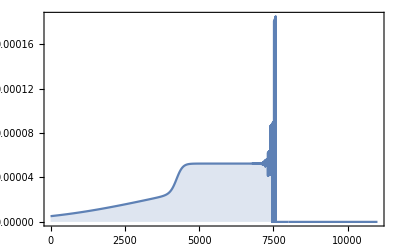

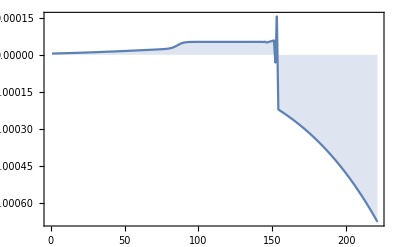

```mathematica
(* Data for Q1*)
u=E^((-(1/(n0+t)-1/(n0+t0))xht)/r0+(xcp(-1+(n0+t0)/(n0+t)+Log[(n0+t)/(n0+t0)]))/r0); 
a=k0 E^(-(((1/(n0+t)-1/(n0+t0))xhl)/r0));
b=1+u+a(p0-h0);
c=-h0(1+u);
y=(-b+Sqrt[b^2-4 a c])/(2 a);
ListLinePlot[Table[y,{t,-10,100,0.1}],PlotRange->All,Frame->True,Filling->Axis]
ListLinePlot[Table[y,{t,-10,100,0.01}],PlotRange->All,Frame->True,Filling->Axis]
ListLinePlot[Table[y,{t,-10,100,0.5}],PlotRange->All,Frame->True,Filling->Axis]
```

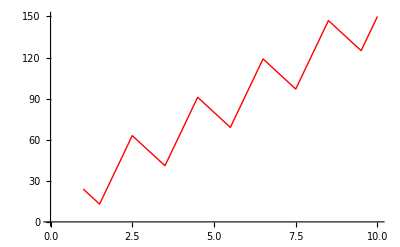

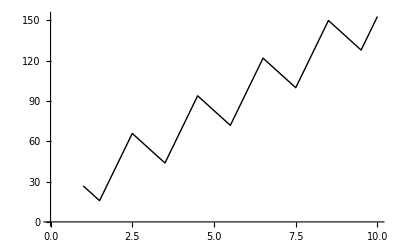

{{1.,5.5,-0.0526316},{5.5,37.75,-0.289474},{-0.0526316,-0.289474,0.473684}}

```mathematica
Y[x_]:=a1 + a2*x + a3 Sin[π*x]
a1=10;
a2=14;
a3=18;
data=Table[{x,Y[x]},{x,1,10,0.5}];
noisedata=RandomVariate[NormalDistribution[.3,4]];
experdata=Table[{x,Y[x]+noisedata},{x,1,10,0.5}];
plt01=ListLinePlot[data, PlotStyle->{Red,Thick}]
plt02=ListLinePlot[experdata, PlotStyle->{Black,Thick}]
a11=1;
a12=Mean[Table[x,{x,1,10,0.5}]];
a13=Mean[Table[Sin[π*x],{x,1,10,0.5}]];
a21=Mean[Table[x,{x,1,10,0.5}]];
a22=Mean[Table[x^2,{x,1,10,0.5}]];
a23=Mean[Table[x*Sin[π*x],{x,1,10,0.5}]];
a31=Mean[Table[Sin[π*x],{x,1,10,0.5}]];
a32=Mean[Table[x*Sin[π*x],{x,1,10,0.5}]];
a33=Mean[Table[Sin[π*x]^2,{x,1,10,0.5}]];
b1=Mean[Table[Y[x],{x,1,10,0.5}]];
b2=Mean[Table[x*Y[x],{x,1,10,0.5}]];
b3=Mean[Table[Y[x]*Sin[π*x],{x,1,10,0.5}]];
M=N[{{a11,a12,a13},{a21,a22,a23},{a31,a32,a33}}];
y={b1,b2,b3};
p=Inverse[M]//MatrixForm;
```

```mathematica
aMnt[mat_, vect_]:= Transpose @ Join[Transpose @ mat, {vect}]
aMat=aMnt[M,y]; aMat//MatrixForm
Module[{i,j,k,tmp=aMat,n=Dimensions[aMat][[1]]},
For[i=1,i<=n-1,i++,
For[j=i+1,j<=n,j++,
pvtFact=N[tmp[[j,i]]/tmp[[i,i]]];
tmp[[j]]=tmp[[j]]-pvtFact*tmp[[i]]]];
matUpT=tmp;]
Map[MatrixForm,{aMat,matUpT}]
n=Dimensions[aMat][[1]]
{upTr,vecB1}={Take[#,All,3],Take[#,3,-1]}&[matUpT]
Map[MatrixForm,{upTr,vecB1}]
```

(1. | 5.5 | -0.0526316 | 86.0526
5.5 | 37.75 | -0.289474 | 578.289
-0.0526316 | -0.289474 | 0.473684 | 3.94737)

{(1. | 5.5 | -0.0526316 | 86.0526
5.5 | 37.75 | -0.289474 | 578.289
-0.0526316 | -0.289474 | 0.473684 | 3.94737),(1. | 5.5 | -0.0526316 | 86.0526
0. | 7.5 | -2.22045×10^-16 | 105.
0. | 0. | 0.470914 | 8.47645)}

3

{{{1.,5.5,-0.0526316},{0.,7.5,-2.22045×10^-16},{0.,0.,0.470914}},{{86.0526},{105.},{8.47645}}}

{(1. | 5.5 | -0.0526316
0. | 7.5 | -2.22045×10^-16
0. | 0. | 0.470914),(86.0526
105.
8.47645)}

```mathematica
(*Gauss Elimination*)
(*Step2*)
Module[{i,j,n=Dimensions[upTr][[1]],vX=Array[x,{n,1}],uP=upTr,vB=vecB1},
vX[[n]]=vB[[n]]/uP[[n,n]];
soln=vX;
Do[vX[[i]]=(vB[[i]]-∑_(j=i+1)^n uP[[i,j]]*vX[[j]])/uP[[i,i]],{i,n-1,1,-1}];
soln=vX;
]
soln
```

{{10.},{14.},{18.}}

```mathematica
(*From the Gauss Elimination method*)

Yg[x_]:=soln[[1,1]]+soln[[2,1]]*x+soln[[3,1]]*Sin[x]
datamanual=Table[{x,Yg[x]}, {x, 1, 10, 0.5}](*Generating data from the Gauss Seidl*)
experimentalData
```

{{1.,39.1465},{1.5,48.9549},{2.,54.3674},{2.5,55.7725},{3.,54.5402},{3.5,52.6859},{4.,52.3776},{4.5,55.4045},{5.,62.7394},{5.5,74.3003},{6.,88.9705},{6.5,104.872},{7.,119.826},{7.5,131.884},{8.,139.808},{8.5,143.373},{9.,143.418},{9.5,141.647},{10.,140.208}}

experimentalData

```mathematica
(*Linear Fit*)
linsolve=LinearSolve[M,y]
linsolve[[2]]
```

{10.,14.,18.}

14.

```mathematica
(*From the Linear Solve*)
Yl[x_]:=linsolve[[1]]+linsolve[[2]]*x+linsolve[[3]]*Sin[x]
dataauto=Table[{x,Yl[x]}, {x, 1, 10, 0.5}]
```

{{1.,39.1465},{1.5,48.9549},{2.,54.3674},{2.5,55.7725},{3.,54.5402},{3.5,52.6859},{4.,52.3776},{4.5,55.4045},{5.,62.7394},{5.5,74.3003},{6.,88.9705},{6.5,104.872},{7.,119.826},{7.5,131.884},{8.,139.808},{8.5,143.373},{9.,143.418},{9.5,141.647},{10.,140.208}}

-Graphics-

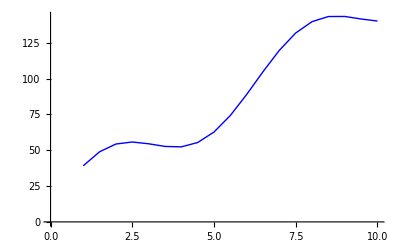

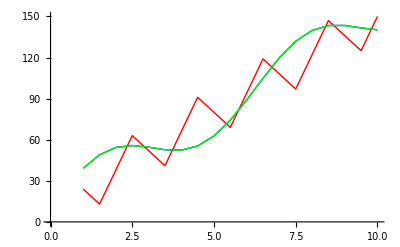

```mathematica
plt1=ListLinePlot[data, PlotStyle->{Red,Thick}];
plt2=ListLinePlot[datamanual, PlotStyle->{Blue,Thick}];
plt3=ListLinePlot[dataauto, PlotStyle->{Green,Thick}];
Show[plt1,plt2,plt3]
Show[plt1,plt2,plt3]
```